```mathematica
P[n_]:= 1/(2^n)/Factorial[n]*D[((x)^2-1)^n,{x,n}]
```

```mathematica
a[n_]:= Integrate[Sin[(Pi*x-Pi)]*P[n],{x,-1,1}]
```

```mathematica
c[n_]:= 2/(2n+1)
```

```mathematica
LegendreExpansion[n_]:= Sum[N[a[n0]/c[n0],20]*P[n0],{n0,0,n}]
```

```mathematica
Sinapprox[x_]=- LegendreExpansion[20]/. x->1-x/Pi ;
```

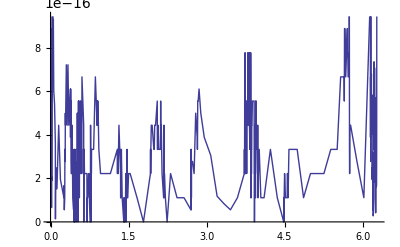

```mathematica
Plot[Abs[Sin[x]-Sinapprox[x]],{x,0,2*Pi}]
```

```mathematica
Export["LegendreCoeff20digits.txt",Table[N[(a[i]/c[i]),20],{i,0,20}]]
```

LegendreCoeff20digits.txt